```mathematica
ClearAll["Global`*"];
r0[a_]:=1/(√(a^2+1))*{{a,0,0,-ⅈ},{0,ⅈ,a,0},{0,a,ⅈ,0},{-ⅈ,0,0,a}};
r0d[a_]:=1/(√(a^2+1))*{{a,0,0,ⅈ},{0,-ⅈ,a,0},{0,a,-ⅈ,0},{ⅈ,0,0,a}};
swap:={{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}};
proj:=1/2*{{1,0,0,1},{0,0,0,0},{0,0,0,0},{1,0,0,1}};
amat=r0[1/(√2)];
amatd=r0d[1/(√2)];
amat//MatrixForm
amatd.amat//MatrixForm//FullSimplify
ConjugateTranspose[amat].amat//MatrixForm//FullSimplify
KP=KroneckerProduct;
```

(1/(√3) | 0 | 0 | -ⅈ √(2/3)
0 | ⅈ √(2/3) | 1/(√3) | 0
0 | 1/(√3) | ⅈ √(2/3) | 0
-ⅈ √(2/3) | 0 | 0 | 1/(√3))

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

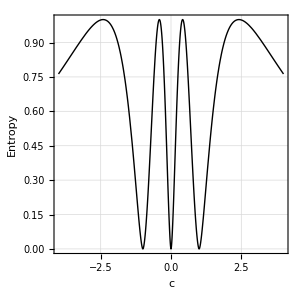

```mathematica
gateEntnew=Plot[entMat = KP[IdentityMatrix[2],proj,IdentityMatrix[2]].KP[r0[c],r0[c]].KP[IdentityMatrix[2],proj,IdentityMatrix[2]];
singularValues=DeleteCases[Diagonal[SingularValueDecomposition[entMat/√Tr[ConjugateTranspose[entMat].entMat]][[2]]],0.];
vn=Total[-singularValues^2.Log[2,singularValues^2]],{c,-4,4},PlotRange->All,PlotTheme->"Scientific",GridLines->Automatic,PlotStyle->{Black,Thick},FrameStyle->Black,AspectRatio->1,ImageSize->300,FrameTicksStyle->18,FrameLabel->{"c","Entropy"},LabelStyle->{18,FontFamily->"Times New Roman"}]
```

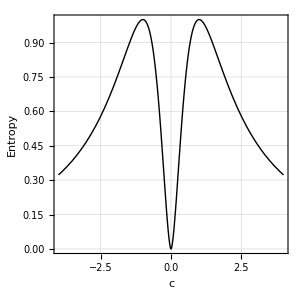

```mathematica
gateEntswap=Plot[entMat = KP[IdentityMatrix[2],proj,IdentityMatrix[2]].KP[r0[100000],r0[c]].KP[IdentityMatrix[2],proj,IdentityMatrix[2]];
singularValues=DeleteCases[Diagonal[SingularValueDecomposition[entMat/√Tr[ConjugateTranspose[entMat].entMat]][[2]]],0.];
vn=Total[-singularValues^2.Log[2,singularValues^2]],{c,-4,4},PlotRange->All,PlotTheme->"Scientific",GridLines->Automatic,PlotStyle->{Black,Thick},FrameStyle->Black,AspectRatio->1,ImageSize->300,FrameTicksStyle->18,FrameLabel->{"c","Entropy"},LabelStyle->{18,FontFamily->"Times New Roman"}]
```